```mathematica
FWHM=2.5;
GaussianSigma=FWHM/2.355;
frameSize=100;
SetDirectory[NotebookDirectory[]];
GaussianPSF[{x1_,y1_},σ_]:=N[PDF[MultinormalDistribution[{x1,y1},{{σ,0},{0,σ}}],{#1,#2}]] 9.42477796076938&;
AiryPSF[{x1_,y1_},σ_]:=N[airy[√((x1-#1)^2+(y1-#2)^2),σ]] 0.7633707592223087 10^4&;
nm=1.0/160.0;
<<"helpers.wls"
<<"level-detection-helpers.wls"

$PlotTheme = "Default";
frameLabelStyle[text_]:= Style[text, FontSize->12,FontColor->Gray];
frameTicksStyle = Directive[FontSize-> 8, FontColor-> Gray];
legendStyle [text_]:= Style[text, FontSize->12, FontColor->Gray];
plotLabelStyle[text_]:= Style[text, FontSize->14, FontColor->Gray];
cm = 72/2.54;
colorMap = 97;

thesisImages = FileNameJoin[{NotebookDirectory[], "..", "..", "thesis","chapters","img"}];
```

## Find Simulation Parameters

Typical values for the EMCCD parameters.

```mathematica
q = 0.92; (* quantum efficiency *)
c = 0.02;  (* spurious charge *)
g = 250; (* gain 250 to 300 *)
r = 50; (* readout noise *)
f = 12.7; (* electrons per image value *)
```

The fluorophore brightness was chosen by adjusting the expected number of photon from a fluorophore so that track levels mean intensity are similar to what is observed in real data sets.

### Find Intensity and Background

```mathematica
adjustParams[20, 5];
```

```mathematica
adjustParams[40, 5];
```

```mathematica
adjustParams[60, 5];
```

```mathematica
adjustParams[80, 5];
```

```mathematica
adjustParams[80, 10];
```

```mathematica
adjustParams[80, 15];
```

```mathematica
adjustParams[80, 20];
```

```mathematica
adjustParams[80, 25];
```

```mathematica
adjustParams[80, 30];
```

### Results

```mathematica
Needs["DatabaseLink`"];
```

```mathematica
<<"../classify-smi/helpers-scores.wls";
<<"../classify-smi/helpers-data.wls";
<<"../classify-smi/scores.wls";
```

```mathematica
conn = OpenSQLConnection[JDBC["PostgreSQL","127.0.0.1/teodor"],"Username"->"teodor"];
```

```mathematica
smi2014records = SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 13
and category = 1
order by source_data_set, source_track_id"
];
```

```mathematica
simIfB05 = <||>;
```

```mathematica
(simIfB05[#] = SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 37
and source_data_set like '%I_"<>numStr[#]<>"%fB_00005%g_250%'
order by source_data_set, source_track_id"] )&/@ Range[20, 80, 20];
```

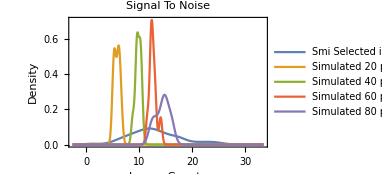

```mathematica
Block[{img},
img = SmoothHistogram[{
SignalToNoiseL1/@smi2014records,
SignalToNoiseL1/@simIfB05[20],
SignalToNoiseL1/@simIfB05[40],
SignalToNoiseL1/@simIfB05[60],
SignalToNoiseL1/@simIfB05[80]},
PlotLabel->plotLabelStyle["Signal To Noise"],
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameLabel-> (frameLabelStyle/@{"Image Counts", "Density"}),
PlotLegends->(legendStyle/@{
"Smi Selected in 2014 L1",
"Simulated 20 photons",
"Simulated 40 photons",
"Simulated 60 photons",
"Simulated 80 photons"}),
ImageSize->10cm];
Export[FileNameJoin[{thesisImages, "methods-simulations-signal-to-noise.pdf"}], img];
img
]
```

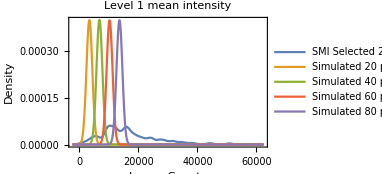

```mathematica
Block[{img},
img = SmoothHistogram[{
#[[scoresI]]["cts_mean_lvl_1"]&/@smi2014records,
#[[scoresI]]["cts_mean_lvl_1"]&/@simIfB05[20],
#[[scoresI]]["cts_mean_lvl_1"]&/@simIfB05[40],
#[[scoresI]]["cts_mean_lvl_1"]&/@simIfB05[60],
#[[scoresI]]["cts_mean_lvl_1"]&/@simIfB05[80]},
1000,
PlotLabel->plotLabelStyle["Level 1 mean intensity"],
Frame-> True,
FrameLabel-> (frameLabelStyle/@{"Image Counts", "Density"}),
FrameTicksStyle->frameTicksStyle,
PlotLegends->(legendStyle/@{"SMI Selected 2014",
"Simulated 20 photons",
"Simulated 40 photons",
"Simulated 60 photons",
"Simulated 80 photons"}),
PlotRange->All,
ImageSize->10cm];
Export[FileNameJoin[{thesisImages, "methods-simulations-l1-intensity.pdf"}],img];
img
]
```

```mathematica
simBfI80 = <||>;
```

```mathematica
(simBfI80[#] = SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 37
and source_data_set like '%I_00080%fB_"<> numStr[#]<>"-q_0_92-c_0_02-g_250-r_50-f_12_7-sigma_1_06157%'
order by source_data_set, source_track_id"] )&/@ Range[5, 30,5];
```

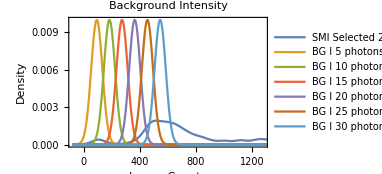

```mathematica
Block[{img},
img = SmoothHistogram[{
Mean/@smi2014records[[All,9,All, 6]],
Mean/@simBfI80[5][[All, 9, All, 6]],
Mean/@simBfI80[10][[All, 9, All, 6]],
Mean/@simBfI80[15][[All, 9, All, 6]],
Mean/@simBfI80[20][[All, 9, All, 6]],
Mean/@simBfI80[25][[All, 9, All, 6]],
Mean/@simBfI80[30][[All, 9, All, 6]]
}, 40,
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameLabel->(frameLabelStyle/@{"Image Counts","Density"}),
PlotLabel->plotLabelStyle["Background Intensity"],
PlotLegends->(legendStyle/@{
"SMI Selected 2014",
"BG I 5 photons",
"BG I 10 photons",
"BG I 15 photons",
"BG I 20 photons",
"BG I 25 photons",
"BG I 30 photons"
}),
ImageSize->10cm];
Export[FileNameJoin[{thesisImages, "methods-simulations-background-int.pdf"}], img];
img
]
```

Based on the histogram of the level 1 signal to noise ratio and level 1 intensity the best value for the fluorophore intensity is 80 photons

Based on the histogram of the background intensity values the best value for the background is 30 photons

Both of these values are at gain 250, A/D factor of 12.7, quantum efficiency of 0.92, spurious charge of 0.02, and read out noise with standard deviation of 50.

### Set Intensity and Background

```mathematica
fI = 80;
fB = 30;
```

## Classification of Single Molecule Data

### Analyzable Tracks

These tracks need to be analysed

#### Helper functions

#### Analyzable Tracks

Generate 3x3 analyzable tracks. Generate a data set with 100, 50, 20, and 10 frames per level. Note that not every track here is in the used class. Some tracks will be rejected by measure_levels2.

```mathematica
exportData[
NotebookDirectory[],
getDataName["an-batch_"<>numStr[#1],Length[#2], fI,fB],
#2
]&@@@ Transpose[{
Flatten@Table[{i, i}, {i, 71,80}],
addNoise[Quiet@generateAnalysable[fI, fB, {
100, 50,
100, 50,
100, 50,
100, 50,
100, 50,
100, 50,
100, 50,
100, 50,
100, 50,
100, 50
}, frameSize, 1]]
}];
```

### Non-Analyzable Tracks

These tracks are not going to be analysed.

```mathematica
fI = 80;
fB = 30;
```

```mathematica
batches = 10;
```

```mathematica
firstBatchId = 11;
```

#### StepRatio

In this simulation the ratio between level 2 and level 1 is different from 2.0

```mathematica
ndata =addNoise@Table[
Print["."];
Block[{
trackNum = 3,
trackDist = 25,
separations = N@{{5nm, 10nm, 15nm}, {20nm, 25nm, 30nm}, {35nm, 40nm, 45nm}},
fIs,
bothOn,
oneOn,
noOn
},
fIs = Flatten[{fI, fI * #}&/@Join[
RandomReal[NormalDistribution[0.5, 0.1], 4],
RandomReal[NormalDistribution[1.7, 0.1], 5]
]
];
bothOn = GenerateFrame[Flatten[Table[{1, 1}, trackNum^2]],fIs,
 Flatten[Table[
{
{x*trackDist, y*trackDist}, 
{x*trackDist+ separations[[x, y]], y*trackDist}
},
{x, 1, trackNum},{y, 1, trackNum}], 2], 
fB, frameSize];
oneOn = GenerateFrame[Flatten[Table[{1, 0}, trackNum^2]],fIs,
Flatten[Table[
{
{x*trackDist, y*trackDist}, 
{x*trackDist+ separations[[x, y]], y*trackDist}
},
{x, 1, trackNum},{y, 1, trackNum}], 2], 
fB, frameSize];
noOn = GenerateFrame[Flatten[Table[{0, 0}, trackNum^2]],fIs, Flatten[Table[
{
{x*trackDist, y*trackDist}, 
{x*trackDist+ separations[[x, y]], y*trackDist}
},
{x, 1, trackNum},{y, 1, trackNum}], 2], 
fB, frameSize];
Join[Table[bothOn, 100], Table[oneOn, 100], Table[noOn, 20]]
],batches];
```

```mathematica
states = Table[
Flatten[{
Table[{1, 1}, 100],
Table[{1, 0}, 100],
Table[{0, 0, 0}, 20]
}, 1],
batches];
```

```mathematica
exportSimulatedData["na-stepratio-batch_", firstBatchId, ndata, states];
```

#### Additional Fluorophore 1

Level 2 is first and Level 1 is last. This data set has a very dim additional fluorophore in level 1, which is active for few more frames after the end of level 1

```mathematica
ndata= addNoise@Table[
Quiet@Block[{
fnum = 3,
fInt = 80,
fAddInt,
fDist,
fSep = 10nm,
fOn, fI, fP,
on3, on2, on1, on0},
fDist =N@ frameSize/(fnum+1);
fAddInt = RandomReal[UniformDistribution[{20, 40}], fnum^2];
fI = Flatten@Table[{fInt, fInt, fAddInt[[i]]}, {i, 1, fnum^2}];
fP = Flatten[Table[{
{x*fDist, y*fDist},
{x*fDist + fSep, y*fDist},
{x*fDist + fSep/2, y*fDist}
}, {x, 1, fnum}, {y, 1, fnum}], 2];
on3= GenerateFrame[Flatten@Table[{1, 1, 1}, fnum^2],fI,fP, fB,frameSize];
on2 = GenerateFrame[Flatten@Table[{1, 0, 1}, fnum^2],fI,fP, fB,frameSize];
on1 = GenerateFrame[Flatten@Table[{0, 0, 1}, fnum^2],fI,fP, fB,frameSize];
on0 = GenerateFrame[Flatten@Table[{0, 0, 0}, fnum^2],fI,fP, fB,frameSize];
Join[Table[on3, 100], Table[on2, 100], Table[on1, 3], Table[on0, 20]]
], batches];
```

```mathematica
states = Table[
Flatten[{
Table[{1, 1, 1}, 100],
Table[{1, 0, 1}, 100],
Table[{0,0,1}, 3],
Table[{0, 0, 0}, 20]
}, 1],
batches];
```

```mathematica
exportSimulatedData["na-add-flfr1-batch_", firstBatchId, ndata, states];
```

#### Additional Fluorophore 2

Level 1 is first and Level 2 is last. This data set has a very dim additional fluorophore in level 1, which is active for few more frames before the beginning of level 1.

```mathematica
ndata= addNoise@Table[
Quiet@Block[{
fnum = 3,
fInt = 80,
fAddInt,
fDist,
fSep = 10nm,
fOn, fI, fP,
on3, on2, on1, on0},
fAddInt = RandomReal[UniformDistribution[{20, 40}], fnum^2];
fDist =N@ frameSize/(fnum+1);
fI = Flatten@Table[{fInt, fInt, fAddInt[[i]]}, {i, 1, fnum^2}];
fP = Flatten[Table[{
{x*fDist, y*fDist},
{x*fDist + fSep, y*fDist},
{x*fDist + fSep/2, y*fDist}
}, {x, 1, fnum}, {y, 1, fnum}], 2];
on3= GenerateFrame[Flatten@Table[{1, 1, 1}, fnum^2],fI,fP, fB,frameSize];
on2 = GenerateFrame[Flatten@Table[{1, 0, 1}, fnum^2],fI,fP,fB,frameSize];
on1 = GenerateFrame[Flatten@Table[{0, 0, 1}, fnum^2],fI,fP,fB,frameSize];
on0 = GenerateFrame[Flatten@Table[{0, 0, 0}, fnum^2],fI,fP,fB,frameSize];
Join[Table[on0, 20], Table[on1,3], Table[on2, 100], Table[on3, 100]]
], 
batches];
```

```mathematica
states = Table[
Flatten[{
Table[{0, 0, 0}, 20],
Table[{0,0,1}, 3],
Table[{1, 0, 1}, 100],
Table[{1, 1, 1}, 100]
}, 1],
batches];
```

```mathematica
exportSimulatedData["na-add-flfr2-batch_", firstBatchId, ndata, states];
```

#### Extrapolated Intensity 1

Level 2 is first and Level 1 is last. Intensity after level 1 for 4 tracks is higher than 0. There is additional undetected fluorophore (Possibly very dim). Intensity after level 1 for 5 tracks is lower than 0. There is a fluorophore in proximity to the feature.

```mathematica
ndata= addNoise@Table[
Quiet@Block[{
fnum = 3,
fInt = 80,
fDist,
fSep = 10nm,
fOn, fI, fP,
on3, on2, on1, on0,
fIntAdd1, fIntAdd2},
fDist =N@ frameSize/(fnum+1);
fIntAdd1 = RandomReal[UniformDistribution[{5,7}], 4];
fIntAdd2 = RandomReal[UniformDistribution[{80, 90}], 5];
fI = Join[
Flatten@Table[{fInt, fInt, fIntAdd1[[i]]},{i, 1, 4}],
Flatten@Table[{fInt, fInt, fIntAdd2[[i]]},{i, 1, 5}]
];
fP = N@Join[
Flatten[Table[{
{x*fDist, y*fDist},
{x*fDist + fSep, y*fDist},
{x*fDist + fSep/2, y*fDist}
}, {x, 1, fnum}, {y, 1, 1}], 2],

Flatten[ {
{{25, 50}, {25 + fSep, 50}, {25 + fSep/2, 50}},
{{50, 50}, {50 + fSep, 50}, {54, 54}},
{{75, 50}, {75 + fSep, 50}, {79, 54}}
}, 1],

Flatten[Table[{
{x*fDist, y*fDist},
{x*fDist + fSep, y*fDist},
{x*fDist + 4, y*fDist +4}
}, {x, 1, fnum}, {y, 3, 3}], 2]
];

on3= GenerateFrame[Flatten@Table[{1, 1, 1}, fnum^2],fI,fP, 30, frameSize];
on2 = GenerateFrame[Flatten@Table[{1, 0, 1}, fnum^2],fI,fP,30, frameSize];
on1 = GenerateFrame[Flatten@Table[{0, 0, 1}, fnum^2],fI,fP,30, frameSize];
on0 = GenerateFrame[Flatten@Table[{0, 0, 0}, fnum^2],fI,fP,30, frameSize];
Join[Table[on3, 100],Table[on2, 100], Table[on1, 20],Table[on0, 20]]
], batches];
```

```mathematica
states = Table[
Flatten[{
Table[{1, 1, 1}, 100],
Table[{1, 0, 1}, 100],
Table[{0,0,1}, 20],
Table[{0, 0, 0}, 20]
}, 1],
batches];
```

```mathematica
exportSimulatedData["na-extr-int1-batch_", firstBatchId, ndata, states];
```

#### Extrapolated Intensity 2

Level 1 is first and Level 2 is last. Intensity before level 1 for 4 tracks is higher than 0. There is additional undetected fluorophore (Possibly very dim). Intensity before level 1 for 5 tracks is lower than 0. There is a fluorophore in proximity to the feature.

```mathematica
ndata= addNoise@Table[
Quiet@Block[{
fnum = 3,
fInt = 80,
fDist,
fSep = 10nm,
fOn, fI, fP,
on3, on2, on1, on0,
fIntAdd1, fIntAdd2},
fDist =N@ frameSize/(fnum+1);
fIntAdd1 = RandomReal[UniformDistribution[{5,7}], 4];
fIntAdd2 = RandomReal[UniformDistribution[{50, 70}], 5];
fI = Join[
Flatten@Table[{fInt, fInt, fIntAdd1[[i]]},{i, 1, 4}],
Flatten@Table[{fInt, fInt, fIntAdd2[[i]]},{i, 1, 5}]
];
fP = N@Join[
Flatten[Table[{
{x*fDist, y*fDist},
{x*fDist + fSep, y*fDist},
{x*fDist + fSep/2, y*fDist}
}, {x, 1, fnum}, {y, 1, 1}], 2],

Flatten[ {
{{25, 50}, {25 + fSep, 50}, {25 + fSep/2, 50}},
{{50, 50}, {50 + fSep, 50}, {54, 54}},
{{75, 50}, {75 + fSep, 50}, {79, 54}}
}, 1],

Flatten[Table[{
{x*fDist, y*fDist},
{x*fDist + fSep, y*fDist},
{x*fDist + 4, y*fDist +4}
}, {x, 1, fnum}, {y, 3, 3}], 2]
];

on3= GenerateFrame[Flatten@Table[{1, 1, 1}, fnum^2],fI,fP, 30, frameSize];
on2 = GenerateFrame[Flatten@Table[{1, 0, 1}, fnum^2],fI,fP, 30, frameSize];
on1 = GenerateFrame[Flatten@Table[{0, 0, 1}, fnum^2],fI,fP, 30, frameSize];
on0 = GenerateFrame[Flatten@Table[{0, 0, 0}, fnum^2],fI,fP, 30, frameSize];
Join[Table[on0, 20], Table[on1,20], Table[on2, 100], Table[on3, 100]]
],batches];
```

```mathematica
states = Table[
Flatten[{
Table[{0, 0, 0}, 20],
Table[{0,0,1}, 20],
Table[{1, 0, 1}, 100],
Table[{1, 1, 1}, 100]
}, 1],
batches];
```

```mathematica
exportSimulatedData["na-extr-int2-batch_",firstBatchId, ndata, states];
```

#### Interruptions

Track has too many interruptions.

```mathematica
states = {};
```

```mathematica
ndata = addNoise@Table[
Quiet@Block[{
trackNum = 3,
trackDist,
on11,on10, on01, on00,
fP
},
trackDist = frameSize/(trackNum + 1);
fP = Flatten[Table[{
{x*trackDist, y*trackDist}, 
{x*trackDist+10nm, y*trackDist}
},{x, 1, trackNum},{y, 1, trackNum}], 2];

on11 = GenerateFrame[
Flatten[Table[{1, 1}, trackNum^2]],
Flatten[Table[{fI, fI}, trackNum^2]],
fP,fB, frameSize];

on10 = GenerateFrame[
Flatten[Table[{1, 0}, trackNum^2]],
Flatten[Table[{fI, fI}, trackNum^2]],
fP,fB, frameSize];

on01 = GenerateFrame[
Flatten[Table[{0, 1}, trackNum^2]],
Flatten[Table[{fI, fI}, trackNum^2]],
fP,fB, frameSize];

on00= GenerateFrame[
Flatten[Table[{0, 0}, trackNum^2]],
Flatten[Table[{fI, fI}, trackNum^2]],
fP,fB, frameSize];

states = Join[
FluorophoresHMM[400, {{0.95, 0.045, 0.005}, {0.2, 0.8, 0}, {0, 0, 1}}],
Table[{0, 0}, 20]
];
Switch[#, {1, 1}, on11, {1, 0}, on10, {0, 1}, on01, {0, 0}, on00]&/@states
],
batches];
```

```mathematica
exportSimulatedData["na-interruptions-batch_",firstBatchId, ndata, states];
```

#### Level 1 2 Gap Intensity

Has intensity in the gap between level 1 and level 2 which is different from the levels. Have 3 tracks with intermediate intensity, 3 with lower than level 1 and 3 with higher than level 2.

```mathematica
ndata = addNoise@Table[
Quiet@Block[{
fnum = 3,
fDist = 25,
fSep = 10nm,
fOn, fI, fP,
level2, btwLevels, level1, noLevel,
fAdd1, fAdd2, fAdd3},
fAdd1 = RandomReal[NormalDistribution[320, 10], 3];
fAdd2 = RandomReal[NormalDistribution[80, 10], 3];
fAdd3 = RandomReal[NormalDistribution[40, 5], 3];
fI = Flatten@Join[{
Table[{160, 160, fAdd1[[i]]},{i, 1,3}],
Table[{160, 160,  fAdd2[[i]]},{i, 1,3}],
Table[{160, 160,  fAdd3[[i]]}, {i, 1,3}]
}];
fP = Flatten[Table[{
{x*fDist, y*fDist},
{x*fDist+fSep, y*fDist},
{x*fDist + fSep/2, y*fDist}},
 {x, 1, fnum}, {y, 1, fnum}], 2];
level2 = GenerateFrame[Flatten@Table[{1, 1, 0},9],
fI, fP, 30, frameSize];

btwLevels = GenerateFrame[Flatten@Join[
Table[{0,1,1},6],
Table[{0,0,1}, 3]
], fI, fP, 30, frameSize];
level1 = GenerateFrame[Flatten[Table[{0, 1, 0}, 9]],
fI, fP, 30, frameSize];

noLevel = GenerateFrame[Flatten@Table[{0,0,0}, 9], fI, fP, 30, frameSize];

Join[Table[level2, 100], Table[btwLevels, 3], Table[level1, 100], Table[noLevel, 20] ]
], batches];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
states = Table[Flatten[{
Table[{1, 1, 0}, 100],
Table[{0, 0, 1}, 3],
Table[{0, 1, 0}, 100],
Table[{0, 0, 0}, 20]
},1], batches];
```

```mathematica
exportSimulatedData["na-lvl12-gap-batch_", firstBatchId, ndata, states];
```

#### Neighbour

There is a fluorophore in the neighbourhood of the diffraction limited spot.

```mathematica
ndata= addNoise@Table[
Quiet@Block[{
fnum = 3,
fInt = 80,
fDist,
fSep = 10nm,
fOn, fI, fP,
on3, on2, on1, on0, fAddI,
angle},

fDist =N@ frameSize/(fnum+1);
fAddI = RandomReal[NormalDistribution[60, 10],fnum^2];
angle = RandomReal[UniformDistribution[{0, 2*Pi}], fnum^2];
fI = Flatten@Table[{fInt, fInt, fAddI[[i]]},{i, 1, fnum^2}];

fP = N@Flatten[Table[{
{x*fDist, y*fDist},
{x*fDist + fSep, y*fDist},
{x*fDist + 5*Cos[angle[[(x-1)*fnum + y]] ], y*fDist +5*Sin[angle[[(x-1)*fnum + y]]]}
}, {x, 1, fnum}, {y, 1, fnum}], 2];

on3= GenerateFrame[Flatten@Table[{1, 1, 1}, fnum^2],fI,fP, 30, frameSize];
on2 = GenerateFrame[Flatten@Table[{1, 0, 1}, fnum^2],fI,fP, 30, frameSize];
on0 = GenerateFrame[Flatten@Table[{0, 0, 0}, fnum^2],fI,fP, 30, frameSize];
Join[ Table[on3, 100],Table[on2, 100], Table[on0, 20]]
], batches];
```

```mathematica
states = Table[Flatten[{
Table[{1, 1, 1}, 100],
Table[{1, 0, 1}, 100],
Table[{0, 0, 0}, 20]
},1], batches];
```

```mathematica
exportSimulatedData["na-neighbour-batch_", firstBatchId, ndata, states];
```

#### Position Shift

There is a change in the position during level 1.

```mathematica
ndata= addNoise@Table[
Quiet@Block[{
fnum = 3,
fInt = 80,
fDist,
fSep = 10nm,
fOn, fI, fP1,fP2,
on2p1, on1p1, on1p2, on0,
offset, offsetI = 1},

fDist =N@ frameSize/(fnum+1);
fI = Join[
Flatten@Table[{fInt, fInt},fnum^2]
];
fP1 = N@Flatten[Table[{
{x*fDist, y*fDist},
{x*fDist + fSep, y*fDist}
}, {x, 1, fnum}, {y, 1, fnum}], 2];
offset = {Cos[#2], Sin[#2]}*#1&@@@Transpose[{
RandomReal[NormalDistribution[80nm, 5nm], 9],
RandomReal[UniformDistribution[{0, 2*Pi}], 9]
}];

fP2 = N@Flatten[Table[{
{x*fDist,y*fDist} + offset[[offsetI++]],
{x*fDist + fSep, y*fDist}
}, {x, 1, fnum}, {y, 1, fnum}], 2];

on2p1 = GenerateFrame[Flatten@Table[{1, 1}, fnum^2],fI,fP1, fB, frameSize];

on1p1 = GenerateFrame[Flatten@Table[{1, 0}, fnum^2],fI,fP1, fB, frameSize];
on1p2 = GenerateFrame[Flatten@Table[{1, 0}, fnum^2],fI,fP2, fB, frameSize];

on0 = GenerateFrame[Flatten@Table[{0, 0}, fnum^2],fI,fP2, fB, frameSize];

Join[ Table[on2p1, 100],Table[on1p1, 50], Table[on1p2,50], Table[on0, 20]]
],batches];
```

```mathematica
states = Table[Flatten[{
Table[{1, 1}, 100],
Table[{1, 0}, 100],
Table[{0, 0}, 20]
},1], batches];
```

```mathematica
exportSimulatedData["na-position-shift-batch_", firstBatchId, ndata, states];
```

### Testing Tracks

#### One Track

This is used for testing of the simulation

```mathematica
data = Block[{bothOn, oneOn, noOn},
bothOn  = GenerateFrame[{1, 1}, {fI, fI},{{20.2, 20.0}, {20.0, 20.2}}, fB, frameSize];
oneOn  = GenerateFrame[{1, 0},{fI, fI},{{20.2, 20.0}, {20.0, 20.2}}, fB, frameSize];
noOn  = GenerateFrame[{0, 0}, {fI, fI}, {{20.2, 20.0}, {20.0, 20.2}}, fB, frameSize];
{Join[Table[bothOn, 100], Table[oneOn, 100], Table[noOn, 20]]}
];
```

```mathematica
MatrixPlot[data⟦1,1⟧]
```

```mathematica
counter = 0;
total = Length@Union@Flatten@data;
```

```mathematica
ndata = addNoise[data];
```

```mathematica
GraphicsRow[{
MatrixPlot[ndata[[1, 1]], PlotRange->All], 
ListPlot3D[ndata[[1, 1]], PlotRange->All]
}]
```

```mathematica
exportData[NotebookDirectory[], "one-track-I10-B1", First@ndata]
```

### Generate Beads

```mathematica
beads = generateBeads[fI,fB, 5, frameSize];
```

Regenerating...36.3372 9.63209 979.584

Regenerating...-7.695330751363026509×10^9 2.128462087793735959×10^9 979.584

Regenerating...207.136 47.9772 1459.71

Regenerating...-110.0607204488860729 2600.851426625005835 1459.71

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

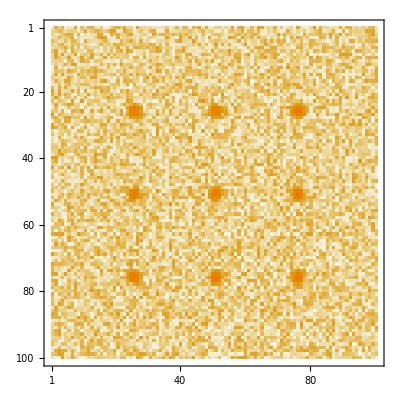

```mathematica
MatrixPlot[beads⟦1,5⟧]
```

```mathematica
exportBeads[FileNameJoin[{NotebookDirectory[],getDataName["beads-100x100", 5, fI, fB]}],beads⟦1⟧];
```

## Level Detection Algorithm

### Training Set

Take 20 samples of each type of data set. These are 60 tracks in total. Add to these tracks 9 with manually chosen level and run the level detection with these samples.

#### Level Changes with Equal Intensity

```mathematica
states = Table[
FluorophoresHMM[400, {{0.98, 0.018, 0.002}, {0.02, 0.98, 0}, {0, 0, 1}}],
 10];
```

```mathematica
ndata = addNoise@generateDataSet[states, 60,120,80];
```

```mathematica
exportSimulatedData["ld-mc-batch_", 41, ndata, states];
```

```mathematica
CloseKernels[];
```

#### Small Intensity Change.

```mathematica
states = Table[
FluorophoresHMM[400, {{0.98, 0.018, 0.002}, {0.02, 0.98, 0}, {0, 0, 1}}],
 10];
```

```mathematica
LaunchKernels[];
```

```mathematica
ndata = addNoise@generateDataSet[states, 30,80,80];
```

```mathematica
CloseKernels[];
```

```mathematica
exportSimulatedData["ld-mc-dim-batch_", 41, ndata, states];
```

#### Short Levels

```mathematica
states = Table[
FluorophoresHMM[400, {{0.92, 0.078, 0.002}, {0.08, 0.92, 0}, {0, 0, 1}}],
 10];
```

```mathematica
LaunchKernels[];
```

```mathematica
ndata = addNoise@generateDataSet[states, 60,120,80];
```

```mathematica
CloseKernels[];
```

```mathematica
exportSimulatedData["ld-mc-short-batch_",41, ndata, states];
```

#### Level Gap Higher Intensity

```mathematica
states = {
Join[Table[{1, 0}, 20], Table[{0, 1}, 3], Table[{0, 0}, 20], Table[{0, 1}, 3],Table[{1, 0}, 20], Table[{1, 1}, 3],Table[{0, 0}, 20],Table[{1, 1}, 3],Table[{1, 0}, 20],Table[{0, 0}, 20],Table[{1, 1}, 3],Table[{0, 1}, 3],Table[{0, 0}, 20],Table[{0, 1}, 3],Table[{1, 1}, 3],Table[{0, 0}, 20],Table[{0, 1}, 3],Table[{1, 0}, 20],Table[{1, 1}, 3],Table[{1, 0}, 20],Table[{0, 1}, 3],Table[{0, 0}, 20],Table[{0, 1}, 3],Table[{1, 0}, 3],Table[{1, 1}, 3],Table[{1, 0}, 3],Table[{0, 1}, 3],Table[{0, 0}, 3]
]
};
```

```mathematica
ndata = addNoise@generateDataSet[states, 120,60,80];
```

```mathematica
exportSimulatedData["ld-lvlgap-batch_", 1, ndata, states];
```

#### Level Gap Lower Intensity

```mathematica
states = {
Join[
Table[{1, 1}, 20],
Table[{0, 1}, 3],
Table[{1, 0}, 20],

Table[{0, 1}, 3],
Table[{0, 0}, 20],
Table[{0, 1}, 3],
Table[{1, 0}, 10],
Table[{0, 1}, 3],
Table[{1, 1}, 10],
Table[{0, 1}, 3],
Table[{1, 0}, 5],
Table[{0, 1}, 3],
Table[{0, 0}, 5]
]
};
```

```mathematica
ndata = addNoise@generateDataSet[states, 120,60,80];
```

```mathematica
exportSimulatedData["ld-lvlgapLI-batch_", 1, ndata, states];
```

### Test Cases

## Display Progress

```mathematica
msg = "None";
counter = 0;
total = 0;
```

```mathematica
Dynamic[{counter, total, msg}]
```

```mathematica
showdata = rawdata;
```

```mathematica
coolcolor[value_, min_, max_]:= RGBColor[#, #, #]&@((value - min)/max);
index = 1;
min = Min@showdata;
max = Max@showdata;
Dynamic@MatrixPlot[showdata⟦1,index⟧,PlotRange->All, ColorFunctionScaling->False,
ColorFunction-> (coolcolor[#,min, max ]&)]
```

```mathematica
Slider[Dynamic[index],{1,Length[showdata[[1]]],1}]
```

```mathematica
cm = 72./2.54;
```

### Thesis images

```mathematica
frame = addNoise[{{GenerateFrame[Table[1, 9], 
Table[120, 9], Flatten[
Table[
{25*x,25*y},
{x, 1, 3}, {y, 1, 3}], 1],
30, 100]
}}];
```

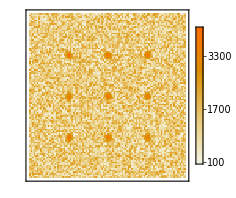

```mathematica
Block[{img},
img = MatrixPlot[First@First@frame,
FrameTicks-> None,
PlotRange->All,
PlotLegends->Automatic,
ImageSize->7cm];
Export[FileNameJoin[{thesisImages,"methods-simulations-typical-frame.pdf"}], img];
img]
```

```mathematica
frameSingleFluorophore = GenerateFrame[{1}, {100},{{9.5, 9.5}}, 30, 20];
```

```mathematica
nframeSingleFluorophore  = First@First@addNoise[{{frameSingleFluorophore }}];
```

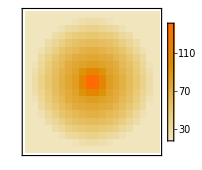
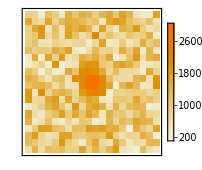

{{1},{{1},118,{{515.727,645.552,676.845,458.035,429.204,458.102,88,624.651,271.525,469.084,485.95,483.989,676.932},98,{1}}}}[1,1,1,1]
 |  |  |  |

```mathematica
Block[{img},
img = Row[{
MatrixPlot[frameSingleFluorophore,
FrameTicks-> None,
PlotRange->All,
PlotLegends->Automatic,
ImageSize->6cm],
MatrixPlot[nframeSingleFluorophore,
FrameTicks-> None,
PlotRange->All,
PlotLegends->Automatic,
ImageSize->6cm]
}];
Export[FileNameJoin[{thesisImages,"methods-simulations-before-after-noise.pdf"}], img];
img]
```